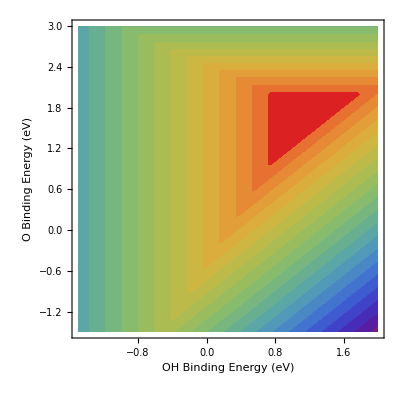

```mathematica
q=(k*T/(2*0.179*10^-3))*(k*T/1)*(2*3.14*32*(10^-3)*k*T/((6.023*10^23)h^2))^1.5;
Emolh2o=-14.699;
Emolh2=-7.036;
Emolo2=-10.54740241;

Ea=1.8*Eo-2.89;
G0=Eo-2*1.23+0.01;
G1=Eoh-Eo+1.23-0.26;
G2=-Eoh+1.23+0.25;
v=k*T/h;
k=8.617343*10^-5;
h=4.13566743*10^-15;
T=298;
ka=Log[v*Exp[-Ea/(k*T)]];
k0=Log[v*Exp[-G0/(k*T)]];
k1=Log[v*Exp[-G1/(k*T)]];
k2=Log[v*Exp[-G2/(k*T)]];
A=k*T*Min[ka,k0,k1,k2];
volcano=ContourPlot[A,{Eoh,-1.5,2},{Eo,-1.5,3},Contours->20,ContourStyle->None,ColorFunction->"Rainbow",Contours->30,Exclusions->None,FrameLabel->{Style["OH Binding Energy (eV)",Large,Black],Style["O Binding Energy (eV)",Large,Black]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18]]
```